```mathematica
Clear["Global`*"]
Needs["Combinatorica`"]
```

```mathematica
(* The Source notebook is avilable in https://resources.wolframcloud.com/FunctionRepository/resources/DominatingIntegerPartitionQ*)
dominationLattice[n_,opts___]:=ResourceFunction["HasseDiagram"][ResourceFunction["DominatingIntegerPartitionQ"],IntegerPartitions[n],opts,VertexShapeFunction->"Name"]

(*Partitions of n up to m integers*)
dominationsubLatticeuptom[n_,m_,opts___]:=ResourceFunction["HasseDiagram"][ResourceFunction["DominatingIntegerPartitionQ"],IntegerPartitions[n, m],opts,VertexShapeFunction->"Name"]
```

## Drawing Young’s diagram

## Only diagrams without dominance ordering

```mathematica
n=8;
IntegerPartitions[n]
Multicolumn[Grid[#,Spacings->{0,0}]&/@Map[Framed,Tableaux[n] /. _Integer->"  "//Union,{3}],8,Appearance->"Horizontal"]
```

{{8},{7,1},{6,2},{6,1,1},{5,3},{5,2,1},{5,1,1,1},{4,4},{4,3,1},{4,2,2},{4,2,1,1},{4,1,1,1,1},{3,3,2},{3,3,1,1},{3,2,2,1},{3,2,1,1,1},{3,1,1,1,1,1},{2,2,2,2},{2,2,2,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

|    |    |    |    |    |    |    |    |    |    |   
   |    |    |    |    |    |    |    |   
   |    |    |  |  |    |    |    |    |    |   
   |    |  |  |  |  |    |    |    |    |    |    |   
   |  |  |  |  |  |  |    |    |   
   |    |   
   |    |  |    |    |    |   
   |    |  | 
   |    |  |  |    |    |    |   
   |    |    | 
   |  |  | 
   |    |    |    |   
   |    |  |  | 
   |  |  |  |  |    |    |    |    |    |   
   |  |  |  |  | 
   |  |  |  |  |  |    |   
   |   
   |   
   |    |    |    |   
   |    | 
   |    | 
   |  |  |    |    |   
   |    |   
   |  | 
   |  |  |    |    |    |   
   |    |  | 
   |  |  | 
   |  |  |  |    |    |    |    |   
   |  |  |  | 
   |  |  |  | 
   |  |  |  |  |    |   
   |   
   |   
   | 
   | 
   |    |   
   |    | 
   |  | 
   |  | 
   |  |  |    |    |    |   
   |  |  | 
   |  |  | 
   |  |  | 
   |  |  |  |    |   
   |   
   | 
   | 
   | 
   |  |    |    |   
   |  | 
   |  | 
   |  | 
   |  | 
   |  |  |    |   
   | 
   | 
   | 
   | 
   | 
   |  |   
  
  
  
  
  
  
   |  |

## Partitions with ordering

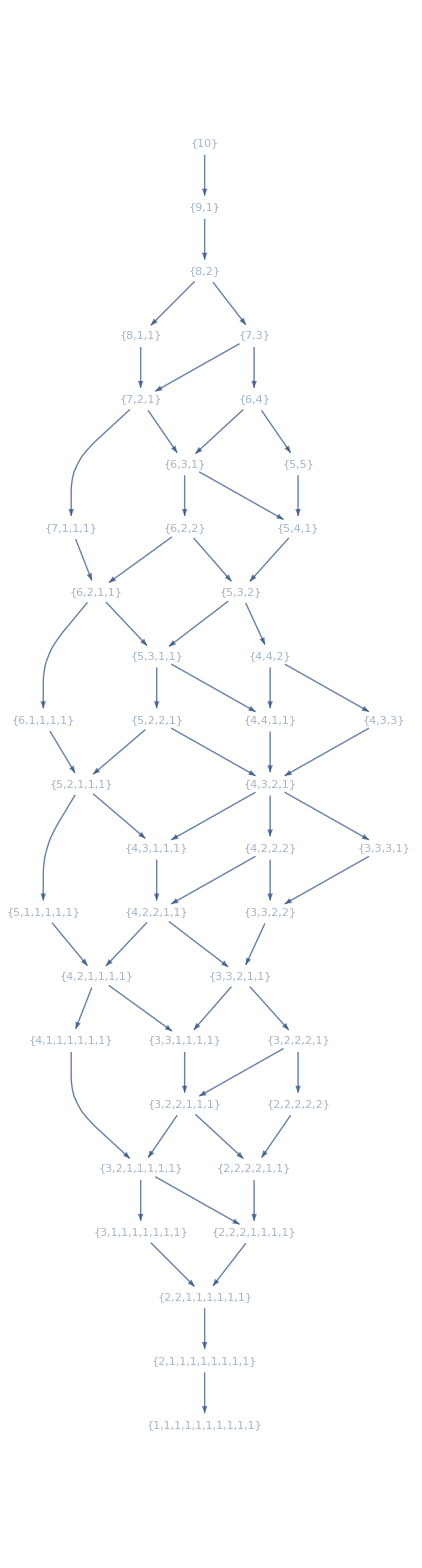

```mathematica
n=10;
dominationLattice[n]
```

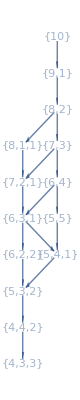

```mathematica
dominationsubLatticeuptom[n, 3]
```

### Check for self - similar structures

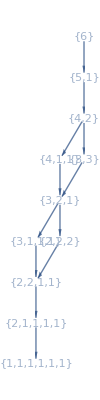

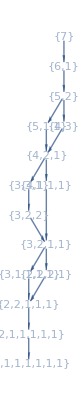

```mathematica
n=6;
dominationLattice[n]
dominationLattice[n+1]
```

## Checking for dominance ordering

```mathematica
ResourceFunction["DominatingIntegerPartitionQ"][{5,1,1,1},{4,3,1}]
```

False